# Simplest Pivoting

The plan is to generate explicit simple pivoting code in Mathematica for Aliyah, Caleb and Josie.

## No Pivoting

Here is the unpivoted function from class

```mathematica
Clear[LUTogether]
LUTogether[A_]:=Module[{m=Length[A],LU=A},
Do[
Do[
LU⟦j,k⟧=LU⟦j,k⟧/LU⟦k,k⟧;
(* Note the diagonals store the U not the L *)
LU⟦j,k+1;;m⟧-=LU⟦j,k⟧ LU⟦k,k+1;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
(* Splitting LU to maintain the return values *)
{LowerTriangularize[LU,-1]+IdentityMatrix[m],UpperTriangularize[LU]}
]
```

I am going to just look at this as a script.

2.28878×10^-16

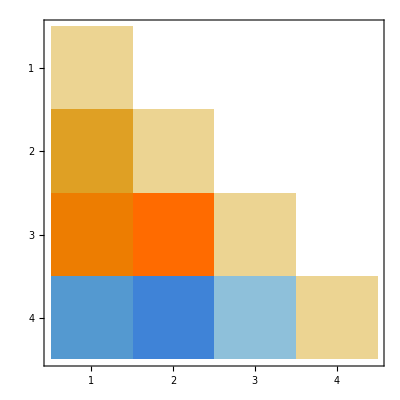
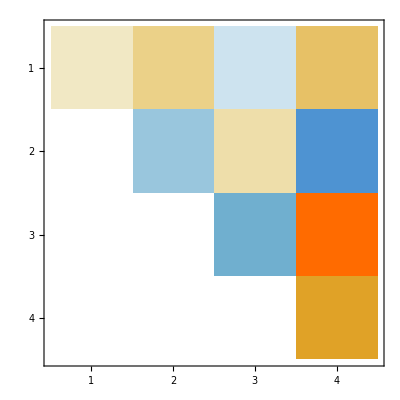

```mathematica
m=4;
A=RandomReal[{-1,1},{m,m}]; b=RandomReal[{-1,1},m];
(* Start Script *)
LU=A;
Do[
Do[
LU⟦j,k⟧=LU⟦j,k⟧/LU⟦k,k⟧;
(* Note the diagonals store the U not the L *)
LU⟦j,k+1;;m⟧-=LU⟦j,k⟧ LU⟦k,k+1;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
(* Splitting LU to maintain the return values *)
{L,U}={LowerTriangularize[LU,-1]+IdentityMatrix[m],UpperTriangularize[LU]};
Norm[A-L.U]
Map[MatrixPlot,{L,U}]
```

## Row Pivoting

We are going to modify this code to do row pivoting.

1.36086×10^-16

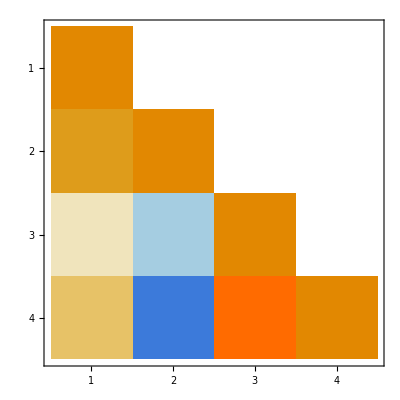
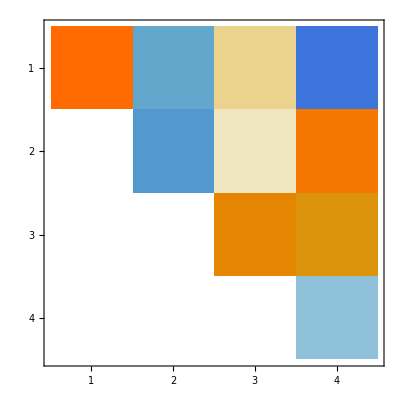

```mathematica
m=4;
A=RandomReal[{-1,1},{m,m}]; b=RandomReal[{-1,1},m];
(* Start Script *)
LU=A;
Do[
(* Add row pivoting stuff here. *)
(* Find pivot row *)
(* record pivot bookkeeping *)
(* Interchange rows in bottom corner *)
Do[
LU⟦j,k⟧=LU⟦j,k⟧/LU⟦k,k⟧;
(* Note the diagonals store the U not the L *)
LU⟦j,k+1;;m⟧-=LU⟦j,k⟧ LU⟦k,k+1;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
(* Splitting LU to maintain the return values *)
{L,U}={LowerTriangularize[LU,-1]+IdentityMatrix[m],UpperTriangularize[LU]};
(* Modify test appropriately *)
Norm[A-L.U]
Map[MatrixPlot,{L,U}]
```

## Column Pivoting

We are going to modify the unpivoted script to do column pivoting.

```mathematica
m=4;
A=RandomReal[{-1,1},{m,m}]; b=RandomReal[{-1,1},m];
(* Start Script *)
LU=A;
Do[
(* Add column pivoting stuff here. *)
(* Find pivot column *)
(* record pivot bookkeeping *)
(* Interchange columns in bottom corner *)
Do[
LU⟦j,k⟧=LU⟦j,k⟧/LU⟦k,k⟧;
(* Note the diagonals store the U not the L *)
LU⟦j,k+1;;m⟧-=LU⟦j,k⟧ LU⟦k,k+1;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
(* Splitting LU to maintain the return values *)
{L,U}={LowerTriangularize[LU,-1]+IdentityMatrix[m],UpperTriangularize[LU]};
(* Modify test appropriately *)
Norm[A-L.U]
Map[MatrixPlot,{L,U}]
```

1.36086×10^-16

{-Graphics-,-Graphics-}

## Complete Pivoting

We are going to modify the unpivoted script to do complete pivoting.

```mathematica
m=4;
A=RandomReal[{-1,1},{m,m}]; b=RandomReal[{-1,1},m];
(* Start Script *)
LU=A;
Do[
(* Add complete pivoting stuff here. *)
(* Find pivot row and column *)
(* record pivot bookkeeping *)
(* Interchange rows and columns in bottom corner *)
Do[
LU⟦j,k⟧=LU⟦j,k⟧/LU⟦k,k⟧;
(* Note the diagonals store the U not the L *)
LU⟦j,k+1;;m⟧-=LU⟦j,k⟧ LU⟦k,k+1;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
(* Splitting LU to maintain the return values *)
{L,U}={LowerTriangularize[LU,-1]+IdentityMatrix[m],UpperTriangularize[LU]};
(* Modify test appropriately *)
Norm[A-L.U]
Map[MatrixPlot,{L,U}]
```

1.36086×10^-16

{-Graphics-,-Graphics-}

## Rook Pivoting

We are looking for a pivot row and column where the appropriate entry is the largest in its row and column.  The literature says the pivot entry dominates the row and column.  We pivot using the first row and column we find.

```mathematica
m=4;
A=RandomReal[{-1,1},{m,m}]; b=RandomReal[{-1,1},m];
(* Start Script *)
LU=A;
Do[
(* Add complete pivoting stuff here. *)
(* Find pivot row and column *)
(* record pivot bookkeeping *)
(* Interchange rows and columns in bottom corner *)
Do[
LU⟦j,k⟧=LU⟦j,k⟧/LU⟦k,k⟧;
(* Note the diagonals store the U not the L *)
LU⟦j,k+1;;m⟧-=LU⟦j,k⟧ LU⟦k,k+1;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
(* Splitting LU to maintain the return values *)
{L,U}={LowerTriangularize[LU,-1]+IdentityMatrix[m],UpperTriangularize[LU]};
(* Modify test appropriately *)
Norm[A-L.U]
Map[MatrixPlot,{L,U}]
```

1.36086×10^-16

{-Graphics-,-Graphics-}